```mathematica
<<MaTeX`
```

## CollinsSoperK . f90

```mathematica
dataIN={{    0.010000,    0.345566,        0.978532,       -0.248283},
{    0.012589,    0.379196,        0.998371,       -0.236311},
{    0.015849,    0.415375,        1.013547,       -0.223903},
{    0.019953,    0.454067,        1.023447,       -0.211028},
{    0.025119,    0.495181,        1.027476,       -0.197653},
{    0.031623,    0.538565,        1.025083,       -0.183743},
{    0.039811,    0.583992,        1.015789,       -0.169259},
{    0.050119,    0.631143,        0.999227,       -0.154161},
{    0.063096,    0.679589,        0.975186,       -0.138405},
{    0.079433,    0.728762,        0.943664,       -0.121948},
{    0.100000,    0.777943,        0.904907,       -0.104747},
{    0.125893,    0.826305,        0.859351,       -0.086755},
{    0.158489,    0.872928,        0.807543,       -0.067928},
{    0.199526,    0.916823,        0.750110,       -0.048220},
{    0.251189,    0.957969,        0.686073,       -0.026942},
{    0.316228,    0.996305,        0.612834,       -0.002704},
{    0.398107,    1.025094,        0.541754,        0.021419},
{    0.501187,    1.045596,        0.469288,        0.047318},
{    0.630957,    1.056037,        0.396908,        0.075348},
{    0.794328,    1.054480,        0.326635,        0.105768},
{    1.000000,    1.040464,        0.264219,        0.136871},
{    1.258925,    1.011380,        0.204439,        0.172388},
{    1.584893,    0.972857,        0.157738,        0.206500},
{    1.995262,    0.921102,        0.116764,        0.244317},
{    2.511886,    0.855369,        0.082038,        0.286843},
{    3.162278,    0.775619,        0.053985,        0.335271},
{    3.981072,    0.682733,        0.032661,        0.391283},
{    5.011872,    0.579132,        0.017707,        0.457239},
{    6.309574,    0.470028,        0.008346,        0.536270},
{    7.943282,    0.365025,        0.003298,        0.632274},
{   10.000000,    0.274212,        0.001047,        0.749593}};
```

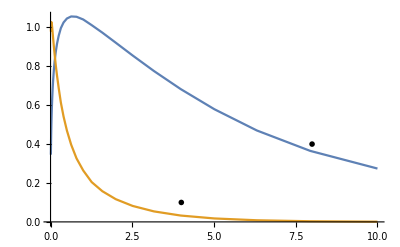

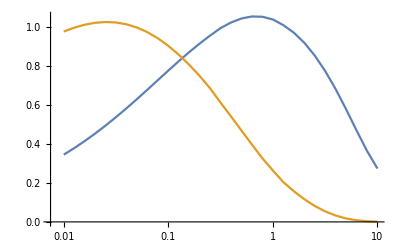

```mathematica
ListPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True,Epilog->{
Inset[MaTeX["R[\\to 4\\text{GeV}]",Magnification->1.4],{8,0.4}],
Inset[MaTeX["R[\\to 91\\text{GeV}]",Magnification->1.4],{4,0.1}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True]
```

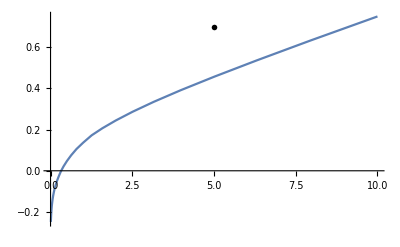

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧},Joined->True,Epilog->{
Inset[MaTeX["\\mathcal{D}(b,4\\text{GeV})",Magnification->1.4],{5,0.7}]
}]
```

## uTMDPDF . f90 (in b)

```mathematica
dataIN={{    0.010000,    8.944884,       12.525273,        3.091052,        4.328314,        8.752856,       12.256381},
{    0.012589,    8.955949,       12.513625,        3.396056,        4.745111,        8.941363,       12.493244},
{    0.015849,    8.964591,       12.497879,        3.723670,        5.191310,        9.086038,       12.667193},
{    0.019953,    8.970377,       12.477478,        4.073149,        5.665607,        9.180704,       12.770035},
{    0.025119,    8.972799,       12.451781,        4.443156,        6.165880,        9.219336,       12.793905},
{    0.031623,    8.971258,       12.420068,        4.831607,        6.689015,        9.196286,       12.731603},
{    0.039811,    8.964974,       12.381460,        5.235474,        7.230674,        9.106525,       12.576956},
{    0.050119,    8.952937,       12.334897,        5.650583,        7.785083,        8.946015,       12.325360},
{    0.063096,    8.933825,       12.279092,        6.071329,        8.344736,        8.712137,       11.974392},
{    0.079433,    8.905844,       12.212442,        6.490242,        8.899965,        8.404129,       11.524447},
{    0.100000,    8.866524,       12.132925,        6.897648,        9.438721,        8.023381,       10.979171},
{    0.125893,    8.812398,       12.037938,        7.281725,        9.947004,        7.572943,       10.344815},
{    0.158489,    8.738534,       11.924065,        7.628115,       10.408856,        7.056744,        9.629198},
{    0.199526,    8.637864,       11.786731,        7.919396,       10.806351,        6.479349,        8.841346},
{    0.251189,    8.500244,       11.619698,        8.142969,       11.131309,        5.831785,        7.971958},
{    0.316228,    8.311232,       11.414282,        8.280523,       11.372107,        5.093407,        6.995063},
{    0.398107,    8.050798,       11.158313,        8.252824,       11.438320,        4.361550,        6.045059},
{    0.501187,    7.692552,       10.834820,        8.043304,       11.328847,        3.610024,        5.084653},
{    0.630957,    7.204792,       10.420475,        7.608525,       11.004405,        2.859637,        4.135967},
{    0.794328,    6.556143,        9.884923,        6.913320,       10.423452,        2.141466,        3.228762},
{    1.000000,    5.728354,        9.192267,        5.960148,        9.564226,        1.513539,        2.428770},
{    1.258925,    4.736054,        8.307912,        4.789952,        8.402457,        0.968233,        1.698460},
{    1.584893,    3.643735,        7.213295,        3.544835,        7.017507,        0.574754,        1.137809},
{    1.995262,    2.562882,        5.929915,        2.360676,        5.462058,        0.299252,        0.692400},
{    2.511886,    1.617854,        4.539314,        1.383861,        3.882786,        0.132725,        0.372395},
{    3.162278,    0.897739,        3.178676,        0.696304,        2.465443,        0.048464,        0.171600},
{    3.981072,    0.426529,        1.998903,        0.291205,        1.364716,        0.013931,        0.065287},
{    5.011872,    0.167518,        1.105741,        0.097015,        0.640370,        0.002966,        0.019579},
{    6.309574,    0.051909,        0.524292,        0.024399,        0.246432,        0.000433,        0.004376},
{    7.943282,    0.011950,        0.205840,        0.004362,        0.075137,        0.000039,        0.000679},
{   10.000000,    0.001894,        0.063911,        0.000519,        0.017525,        0.000002,        0.000067}};
```

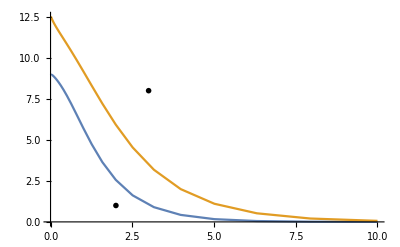

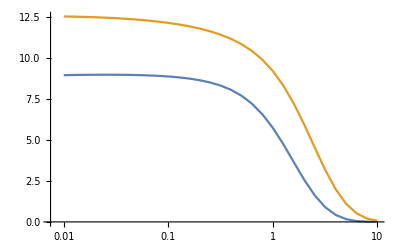

```mathematica
ListPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True]
```

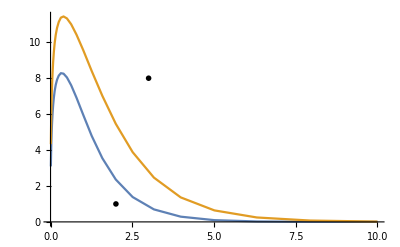

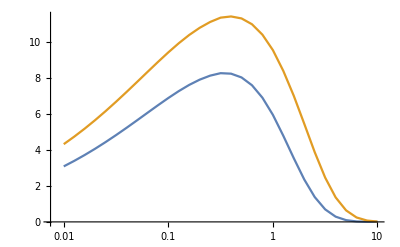

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True]
```

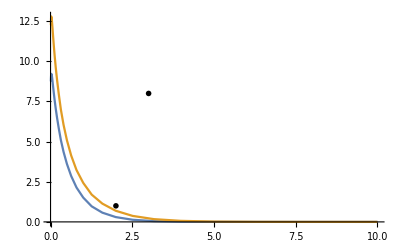

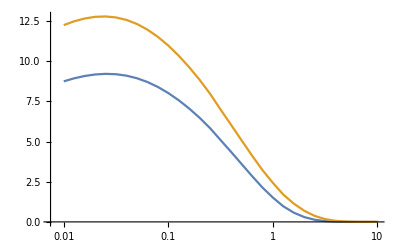

```mathematica
ListPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True]
```

## uTMDPDF . f90 (in kT)

```mathematica
dataIN={{    0.010000,    2.869285,        8.985124,        2.519290,        6.760045,        0.478725,        0.906423},
{    0.012589,    2.868959,        8.982594,        2.519074,        6.758823,        0.478709,        0.906370},
{    0.015849,    2.868444,        8.978587,        2.518731,        6.756887,        0.478683,        0.906286},
{    0.019953,    2.867628,        8.972242,        2.518187,        6.753821,        0.478642,        0.906154},
{    0.025119,    2.866335,        8.962199,        2.517327,        6.748966,        0.478577,        0.905944},
{    0.031623,    2.864288,        8.946321,        2.515964,        6.741282,        0.478474,        0.905611},
{    0.039811,    2.861048,        8.921247,        2.513805,        6.729134,        0.478311,        0.905084},
{    0.050119,    2.855925,        8.881738,        2.510391,        6.709952,        0.478054,        0.904251},
{    0.063096,    2.847836,        8.819695,        2.504993,        6.679729,        0.477646,        0.902932},
{    0.079433,    2.835090,        8.722777,        2.496476,        6.632273,        0.477001,        0.900850},
{    0.100000,    2.815074,        8.572636,        2.483067,        6.558156,        0.475981,        0.897568},
{    0.125893,    2.783809,        8.343025,        2.462041,        6.443365,        0.474374,        0.892410},
{    0.158489,    2.735376,        7.998773,        2.429273,        6.267868,        0.471846,        0.884347},
{    0.199526,    2.661311,        7.497858,        2.378691,        6.004815,        0.467890,        0.871837},
{    0.251189,    2.550274,        6.800344,        2.301762,        5.622049,        0.461743,        0.852663},
{    0.316228,    2.388711,        5.887632,        2.187384,        5.088693,        0.452296,        0.823811},
{    0.398107,    2.163749,        4.789085,        2.023004,        4.389513,        0.438024,        0.781589},
{    0.501187,    1.869452,        3.599502,        1.798185,        3.545451,        0.417013,        0.722273},
{    0.630957,    1.515539,        2.462310,        1.511369,        2.628648,        0.387235,        0.643615},
{    0.794328,    1.133036,        1.514221,        1.177973,        1.752640,        0.347249,        0.547078},
{    1.000000,    0.768634,        0.829394,        0.833333,        1.030659,        0.297328,        0.439566},
{    1.258925,    0.466589,        0.402714,        0.523194,        0.524829,        0.240493,        0.332540},
{    1.584893,    0.250320,        0.174807,        0.284012,        0.225632,        0.182405,        0.237787},
{    1.995262,    0.117344,        0.070751,        0.127851,        0.077125,        0.129521,        0.162483},
{    2.511886,    0.047821,        0.029270,        0.042962,        0.015744,        0.086491,        0.107369},
{    3.162278,    0.017297,        0.013524,        0.005762,       -0.005289,        0.054707,        0.068822},
{    3.981072,    0.006028,        0.006939,       -0.006296,       -0.010678,        0.032884,        0.042331},
{    5.011872,    0.002318,        0.003724,       -0.007948,       -0.010333,        0.018847,        0.024808},
{    6.309574,    0.001038,        0.002017,       -0.006299,       -0.007889,        0.010648,        0.014389},
{    7.943282,    0.000504,        0.001093,       -0.004295,       -0.005374,        0.006127,        0.008537},
{   10.000000,    0.000247,        0.000591,       -0.002973,       -0.003820,        0.003177,        0.004462}};
```

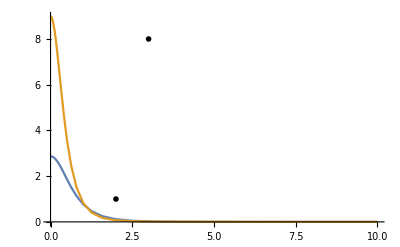

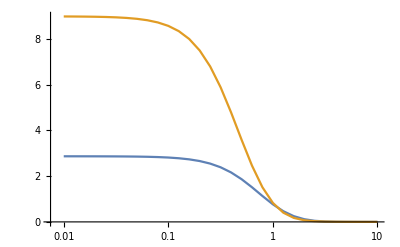

```mathematica
ListPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,2}⟧,dataIN⟦All,{1,3}⟧},Joined->True]
```

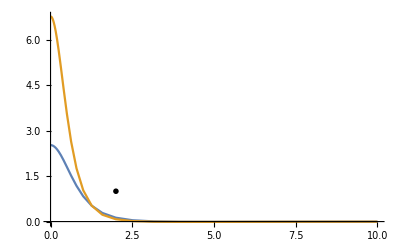

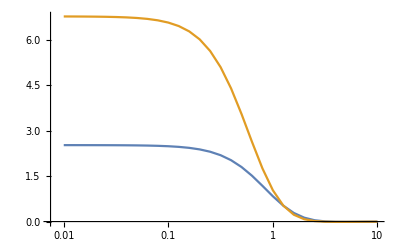

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True]
```

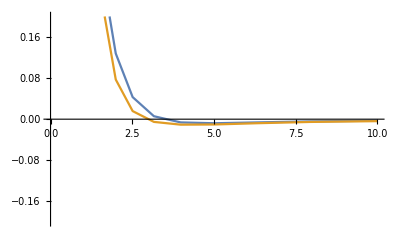

```mathematica
ListPlot[{dataIN⟦All,{1,4}⟧,dataIN⟦All,{1,5}⟧},Joined->True,PlotRange->{All,{-0.2,0.2}}]
```

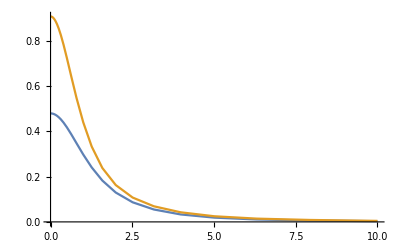

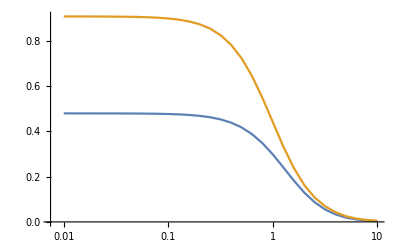

```mathematica
ListPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True,Epilog->{
Inset[MaTeX["d-quark",Magnification->1.4],{2,1}],
Inset[MaTeX["u-quark",Magnification->1.4],{3,8}]
}]
ListLogLinearPlot[{dataIN⟦All,{1,6}⟧,dataIN⟦All,{1,7}⟧},Joined->True]
```